```mathematica
Manipulate[Module[{sol,ACp,PDEp,cAMP,t},sol=NDSolve[{
ACp'[t]==r1*cAMP[t]*((ACt-ACp[t])/(K1))-r2*Dt*ACp[t]/(K2+ACp[t]),PDEp'[t]==r3*cAMP[t]*((PDEt-PDEp[t])/(K3))-r4*Et*(PDEp[t])/(K4+PDEp[t]),cAMP'[t]==(k1*(ACp[t]))-(k3+k4*(PDEp[t]))*cAMP[t],
ACp[0]==x0[[1]],PDEp[0]==x0[[2]],cAMP[0]==x0[[3]]},{ACp,PDEp,cAMP},{t,0,500}];
Plot[Evaluate[{ACp[t],PDEp[t],cAMP[t]}/. sol],{t,0,500},PlotRange->All,PlotLegends->{"ACp(t)","PDEp(t)","cAMP(t)"},AxesLabel->{"Time","Concentration"}]],
{{k1,2.85},0,10,Appearance->"Labeled"},
{{k3,0.69},0,10,Appearance->"Labeled"},
{{k4,4.45},0,10,Appearance->"Labeled"},
{{r1,0.52},0,10,Appearance->"Labeled"},
{{r2,0.47},0,10,Appearance->"Labeled"},
{{r3,2},0,10,Appearance->"Labeled"},
{{r4,10},0,10,Appearance->"Labeled"},
{{Et,0.28},0,10,Appearance->"Labeled"},
{{Dt,0.15},0,10,Appearance->"Labeled"},
{{K1,0.1},0,10,Appearance->"Labeled"},
{{K2,0.1},0,10,Appearance->"Labeled"},
{{K3,0.001},0,10,Appearance->"Labeled"},
{{K4,1},0,10,Appearance->"Labeled"},
{{ACt,0},0,10,Appearance->"Labeled"},
{{PDEt,0},0,10,Appearance->"Labeled"},{{x0,{0.33,0.33,0.33}},Appearance->"Labeled"},Button["Randomize Parameters",k0=RandomReal[{-10,10}];
k1=RandomReal[{0,10}];
k3=RandomReal[{0,10}];
k4=RandomReal[{0,10}];
r1=RandomReal[{0,10}];
r2=RandomReal[{0,10}];
r3=RandomReal[{0,10}];
r4=RandomReal[{0,10}];
Et=RandomReal[{0,10}];
Dt=RandomReal[{0,10}];
K1=RandomReal[{0,10}];
K2=RandomReal[{0,10}];
K3=RandomReal[{0,10}];
K4=RandomReal[{0,10}];
ACt=RandomReal[{0,10}];
PDEt=RandomReal[{0,10}]],TrackedSymbols->{k0,k1,k3,k4,r1,r2,r3,r4,Et,Dt,K1,K2,K3,K4,q1,q2,x0}
]
```

NDSolve::nderr: Error test failure at t$646324 == 37.1571; unable to continue.

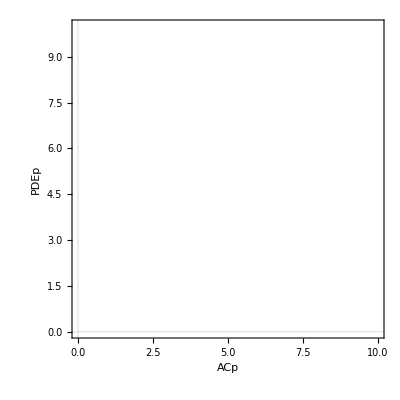

```mathematica
(*Constants*)r1=0.98;r2=4.48;r3=1;r4=1;
K1=1;K2=1;K3=1;K4=1;
k1=1;k3=1;k4=1;
ACt=1;PDEt=1;Dval=1;Evalue=1;

(*ODEs*)odeACp=r1*camp*((ACt-ACp)/(K1))-r2*Dvalue*ACp/(K2+ACp);
odePDEp=r3*camp*((PDEt-PDEp)/(K3))-r4*Evalue*(PDEp)/(K4+PDEp);
odecAMP=(k1*(ACp))-(k3+k4*(PDEp))*camp;

(*Nullcline Equations*)
nullclineACp=odeACp==0;
nullclinePDEp=odePDEp==0;
nullclinecAMP=odecAMP==0;

(*Eliminate camp from nullcline equations*)
eliminatedEquation=Eliminate[{nullclineACp,nullclinePDEp,nullclinecAMP},camp];

(*Plotting the nullclines*)
ContourPlot[Evaluate[eliminatedEquation],{ACp,0,10},{PDEp,0,10},FrameLabel->{"ACp","PDEp"},PlotTheme->"Scientific",ContourStyle->{Red,Green,Blue}]
```